```mathematica
Needs["HierarchicalClustering`"]
SetOptions[{Plot,MatrixPlot},ImageSize->250{1,1}];
```

```mathematica
tmax=60;ϵ=5;δ=6;γ=1;μ=1;
T1=1;
nlo1=NDSolveValue[{μ y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==γ Cos[t/T1],y[0]==1,y'[0]==0},y,{t,0,tmax}]
nlo2=NDSolveValue[{μ y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==γ Cos[t/T2[t]],y[0]==1,y'[0]==0,T2[0]==1.,WhenEvent[t>50,T2[t]->2T2[t]]},y,{t,0,tmax},DiscreteVariables->T2]
```

InterpolatingFunction[{{0., 60.}}, <>]

InterpolatingFunction[{{0., 60.}}, <>]

```mathematica
With[{stepSize=0.08,end=tmax,nn=0.001},
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo1[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]

MatrixPlot[UnitStep[nn-DistanceMatrix[nlo2[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]
]
```

-Graphics- -Graphics-

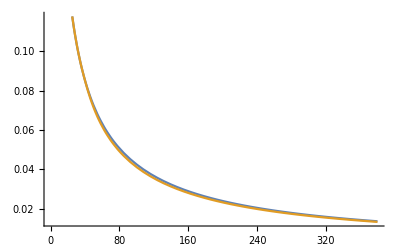

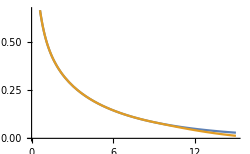

```mathematica
Clear[tmax,ϵ,δ,γ,μ];
tmax=380.;ϵ=3.;δ=6.;γ=0.;μ=1.;
T1=10.;T2=1; n=2;
nlo1=NDSolveValue[{μ y''[t]+δ y'[t]+(y[t])^n+ϵ (y[t])^3==(γ Sin[t/T1])Sin[ t/T2],y[0]==1,y'[0]==0},y,{t,0,tmax}];
nlo2=NDSolveValue[{μ2[t] y''[t]+δ y'[t]+(y[t])^n+ϵ (y[t])^3==γ Sin[t/T1]Sin[t/T2],y[0]==1,y'[0]==0,μ2[0]==1.,WhenEvent[t>0.1tmax,μ2[t]->15μ2[t]]},y,{t,0,tmax},DiscreteVariables->μ2];

Plot[{nlo1[t],nlo2[t]},{t,0,tmax}]
```

```mathematica
With[{stepSize=0.08,end=tmax,nn=0.0001},
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo1[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo2[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]
]
```

-Graphics- -Graphics-